# Final Exam

## Question 1:

```mathematica
f[x_]:= Piecewise[{{x+2/3, 0 ≤ x≤ 1/3}, {-3x+2, 1/3 ≤  x ≤ 2/3}, {2(x-2/3), 2/3 ≤ x≤ 1}, {Undefined, True}}]
```

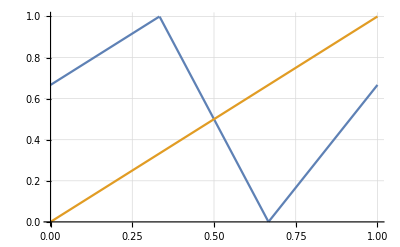

```mathematica
Plot[{f[x], x}, {x, 0, 1}, GridLines->Automatic]
```

```mathematica
partitions = {{0, 1/3}, {1/3, 2/3}, {2/3, 1}};
```

```mathematica
Map[f, partitions, {2}] //MatrixForm
```

(2/3 | 1
1 | 0
0 | 2/3)

The topological transition matrix is given by

```mathematica
A = {{0, 0, 1}, {1, 1, 1}, {1, 1, 0}};
A // MatrixForm
```

(0 | 0 | 1
1 | 1 | 1
1 | 1 | 0)

```mathematica
Abs[f'[x]] // Simplify
```

ConditionalExpression[Piecewise[{{1, 0<x<1/3}, {2, 2/3<x<1}, {3, 1/3<x<2/3}, {Indeterminate, True}}], 0≤x≤1]

The map is expanding and piecewise linear.

#### Next, we compute the number of periodic points of period p=1,2,3 of the map

```mathematica
A // MatrixForm
```

(0 | 0 | 1
1 | 1 | 1
1 | 1 | 0)

```mathematica
MatrixPower[A, 2] // MatrixForm
```

(1 | 1 | 0
2 | 2 | 2
1 | 1 | 2)

```mathematica
MatrixPower[A, 4] // MatrixForm
```

(3 | 3 | 2
8 | 8 | 8
5 | 5 | 6)

#### We determine all admissible period sequences of period 2

```mathematica
Solve[f[f[x]] == x, x]
```

{{x→0},{x→8/21},{x→1/2},{x→2/3},{x→6/7}}

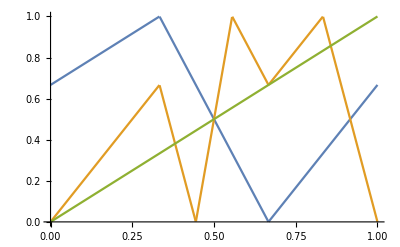

```mathematica
Plot[{f[x],f[f[x]],x}, {x, 0, 1}]
```

### Determine the transfer matrix of the map and compute the invariant density

First, we compute the transfer matrix of the map

```mathematica
slopes = {1, 3,2};
T = Transpose[(A / slopes)];
T // MatrixForm
```

(0 | 1/3 | 1/2
0 | 1/3 | 1/2
1 | 1/3 | 0)

Make sure that has an eigenvalue of 1

```mathematica
Eigenvalues[T]
```

{1,-2/3,0}

Compute the solution to the invariant density

```mathematica
eigvec = {Subscript[ρ, 0], Subscript[ρ, 1], Subscript[ρ, 2]};
intSize = {1, 1, 1} / 3;
```

```mathematica
Solve[T . eigvec == eigvec && eigvec . intSize == 1, eigvec]
```

{{ρ_0→9/10,ρ_1→9/10,ρ_2→6/5}}

```mathematica
p[x_] := Piecewise[{{9/10, 0 ≤ x≤ 1/3}, {9/10, 1/3 ≤  x ≤ 2/3}, {6/5, 2/3 ≤ x≤ 1}, {Undefined, True}}]
```

### Lyapunov exponent of the system

Compute the Lyapunov exponent for the system

```mathematica
Λmap = Integrate[Log[Abs[f'[x]]] p[x], {x,0,1}]
```

1/10 (4 Log[2]+3 Log[3])

### Topological Entropy

Next, we compute the topological entropy of the system

```mathematica
Eigenvalues[MatrixPower[A, 10]]
```

{1024,1,0}

```mathematica
Eigenvalues[A] ^ 10
```

{1024,1,0}

```mathematica
Eigenvalues[A]
```

{2,-1,0}

```mathematica
Log[2] // N
```

0.693147

```mathematica
Log[2] - Λmap  // N
```

0.0863046

### Choosing a different map for which the Lyapunov exponent equals the topological entropy

```mathematica
f1[x_] = Piecewise[{{2x, 0≤x≤ 1/2}, {2-2x, 1/2 <x≤ 1}, {Undefined, True}}];
```

```mathematica
A1 = {{1,1}, {1,1}}
```

{{1,1},{1,1}}

Computing the transfer Matrix

```mathematica
slopes = {2,2}
```

{2,2}

```mathematica
T1 = Transpose[(A1 / slopes)];
T1 // MatrixForm
```

(1/2 | 1/2
1/2 | 1/2)

```mathematica
Eigenvalues[T1]
```

{1,0}

```mathematica
intSize = {1, 1}/2;
```

```mathematica
eigvec = {Subscript[ρ, 0], Subscript[ρ, 1]};
```

```mathematica
Solve[T1 . eigvec == eigvec && eigvec . intSize == 1, eigvec]
```

{{ρ_0→1,ρ_1→1}}

```mathematica
p1[x_] = Piecewise[{{1, 0≤x≤ 1/2}, {1, 1/2 <x≤ 1}, {Undefined, True}}];
```

```mathematica
Integrate[Log[Abs[f1'[x]]] p1[x], {x,0,1}]
```

Log[2]

```mathematica
Eigenvalues[A]
```

{2,-1,0}

## Question 2

We find the inverse branches and the derivatives

```mathematica
f[x_] := 1-2 x^2;
Solve[f[y] == x, y]
```

{{y→-(√(1-x))/(√2)},{y→(√(1-x))/(√2)}}

```mathematica
ϕ1[x_] = -(√(1-x))/(√2);
ϕ2[x_] = (√(1-x))/(√2);
```

Next, we show that ρ is a solution to the Frobenius-Perron equation.  Hence, it is a “valid” invariant density

```mathematica
ρ[x_] = c/(√(1-x^2));
```

```mathematica
Abs[ϕ1'[x]] ρ[ϕ1[x]] + Abs[ϕ2'[x]] ρ[ϕ2[x]] // Simplify
```

c/(√(1+x) √Abs[1-x])

Next, we show that ρ0 is not a solution to the FP equation

```mathematica
ρ0[x_] = c (1+x^2);
```

```mathematica
Abs[ϕ1'[x]] ρ0[ϕ1[x]] + Abs[ϕ2'[x]] ρ0[ϕ2[x]] // Simplify
```

-(c (-3+x))/(2 √2 √Abs[1-x])

C

```mathematica
f[x_] := 4(x+1/2)(1-x-1/2);
Solve[f[y] == x, y]
```

{{y→-(√(1-x))/2},{y→(√(1-x))/2}}

```mathematica
ϕ1[x_] = -(√(1-x))/(√2);
ϕ2[x_] = (√(1-x))/(√2);
```

```mathematica
Abs[ϕ1'[x]] ρ[ϕ1[x]] + Abs[ϕ2'[x]] ρ[ϕ2[x]] // Simplify
```

c/(√(1+x) √Abs[1-x])

We find the normalization constant of the invariant density

```mathematica
Integrate[1/(√(1-x^2)), {x, -1, 1}]
```

π

Computing the time-average for a function h(x)=(1-x^2)^(5/2)

```mathematica
Integrate[(1-x^2)^(5/2)1/(π √(1-x^2)), {x, -1, 1}]
```

16/(15 π)

#### Extra: finding another map with the same invariant density

```mathematica
ρ[x_] := c/(√(1-x^2));
f[x_] :=1-2 x^2;
Solve[f[y] == x, y];
{ϕ1[x_],ϕ2[x_]}= Solve[f[y] == x, y][[All,1,-1]];
Abs[ϕ1'[x]] ρ[ϕ1[x]] + Abs[ϕ2'[x]] ρ[ϕ2[x]] // Simplify
```

c/(√(1+x) √Abs[1-x])

```mathematica
f[x_] :=2 x^2-1;
Solve[f[y] == x, y];
{ϕ1[x_],ϕ2[x_]}= Solve[f[y] == x, y][[All,1,-1]];
Abs[ϕ1'[x]] ρ[ϕ1[x]] + Abs[ϕ2'[x]] ρ[ϕ2[x]] // Simplify
```

c/(√(1-x) √Abs[1+x])

The following two maps have the same invariant density. Note how their inverse branches differ

```mathematica
Solve[4y(1-y) == x, y]
```

{{y→1/2 (1-√(1-x))},{y→1/2 (1+√(1-x))}}

```mathematica
Solve[(2y-1)^2 == x, y]
```

{{y→1/2 (1-√x)},{y→1/2 (1+√x)}}

```mathematica
ϕ1[x_] := 1/2 (1-√x);
ϕ2[x_] :=1/2 (1-√x);
```

```mathematica
ρ[x_] := c/(√(x(1-x)));
```

```mathematica
Abs[ϕ1'[x]] ρ[ϕ1[x]] + Abs[ϕ2'[x]] ρ[ϕ2[x]] // Simplify
```

c/(√(1-x) √Abs[x])

Comparing the previous result, we find a map that slightly diverges

```mathematica
Solve[(√x)/2 == y,x]
```

{{x→4 y^2}}

```mathematica
1 /(√(2-x)√x )
```

1/(√(2-x) √x)

## Question 3

```mathematica
fm[x_] := x - x^3
```

```mathematica
Solve[fm[x] == 0, x]
```

{{x→-1},{x→0},{x→1}}

```mathematica
fm'[{0,1, -1}]
```

{1,-2,-2}

Computing the Laplacian Matrix and determining the eigenvalues

```mathematica
A = {{0, 1, 1, 1}, {1, 0, 1, 0}, {1, 1, 0, 1}, {1, 0, 1, 0}};
A // MatrixForm
```

(0 | 1 | 1 | 1
1 | 0 | 1 | 0
1 | 1 | 0 | 1
1 | 0 | 1 | 0)

```mathematica
G = DiagonalMatrix[Total[A, {2}]] - A;
G // MatrixForm
```

(3 | -1 | -1 | -1
-1 | 2 | -1 | 0
-1 | -1 | 3 | -1
-1 | 0 | -1 | 2)

```mathematica
Eigenvalues[G]
```

{4,4,2,0}

```mathematica
Factor[Det[G - λ IdentityMatrix[4]]]
```

(-4+λ)^2 (-2+λ) λ

The value I got manually

```mathematica
3(2-λ)(λ-4) + (2-λ)(3-λ)((2-λ)(3-λ)-1) + (2-λ)(λ-3) // Simplify
```

(-4+λ)^2 (-2+λ) λ

Computing the conditions for transversal stability

```mathematica
Reduce[{fm'[0] + 4σ < 0, fm'[0] + 2σ < 0}, σ]
```

σ<-1/2

```mathematica
Reduce[{fm'[2] + 4σ < 0, fm'[2] + 2σ < 0}, σ]
```

σ<11/4

```mathematica
Reduce[{fm'[-1] + 4σ < 0, fm'[-1] + 2σ < 0}, σ]
```

σ<1/2

```mathematica
fm'[2]
```

-11

```mathematica
Solve[fm[x] == 0,x]
```

{{x→-1},{x→0},{x→1}}